THIS NOTEBOOK PROVIDES A SET OF TESTS FOR THE BELIEFPROPAGATION.WL PACKAGE ALGORITHMS
© Copyright Stuart Nettleton 2020
Disclaimer: This software is provided without any warranty express or implied Stuart Nettleton 2020
Requires Wolfram Mathematica 12.1.0.0 or higher
All code files and executable documents are with the license GPL 3.0.For details see http://www.gnu.org/licenses/.
All documents are with the license Creative Commons Attribution 4.0 International (CC BY 4.0). For details see https://creativecommons.org/licenses/by/4.0/.
Based on a scheme provided by Daphne Koller in the Stanford University Subject Probabilistic Graphical Models, Copyright (C) Daphne Koller, Stanford University, 2012

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
<<beliefPropagation.wl
datadirectory="beliefPropagationTestData/";
Print[Style["EXACT BELIEF PROPAGATION",{Larger,Red,Bold}]];
indexToAssignmentInput=Get[datadirectory<>"indexToAssignmentInput.txt"];
indexToAssignmentOutput=Get[datadirectory<>"indexToAssignmentOutput.txt"];
Print["indexToAssignment test: ",indexToAssignment@@indexToAssignmentInput==indexToAssignmentOutput]
assignmentToIndexInput=Get[datadirectory<>"assignmentToIndexInput.txt"];
assignmentToIndexOutput=Get[datadirectory<>"assignmentToIndexOutput.txt"];
Print["assignmentToIndex test: ",assignmentToIndex@@#&/@assignmentToIndexInput==assignmentToIndexOutput]
factorProductOrSumInput1=Get[datadirectory<>"factorProductOrSumInput1.txt"];
factorProductOrSumOutput1=Get[datadirectory<>"factorProductOrSumOutput1.txt"];
Print["Factor Product Sum Test 1 ... ",factorProductOrSum[##,False]&@@factorProductOrSumInput1==factorProductOrSumOutput1]
factorProductOrSumInput2=Get[datadirectory<>"factorProductOrSumInput2.txt"];
factorProductOrSumOutput2=Get[datadirectory<>"factorProductOrSumOutput2.txt"];
Print["Factor Product Sum Test 2 ... ",factorProductOrSum[##,False]&@@factorProductOrSumInput2[[;;2]]==factorProductOrSumOutput2]
factorMarginalizationInput1=Get[datadirectory<>"factorMarginalizationInput1.txt"];
factorMarginalizationOutput1=Get[datadirectory<>"factorMarginalizationOutput1.txt"];
Print["Factor Marginalization Sum Test 1 ... ",factorMarginalization[##,False]&@@factorMarginalizationInput1==factorMarginalizationOutput1]
factorMarginalizationInput2=Get[datadirectory<>"factorMarginalizationInput2.txt"];
factorMarginalizationOutput2=Get[datadirectory<>"factorMarginalizationOutput2.txt"];
Print["Factor Marginalization Max Test 2... ",factorMarginalization[##,True]&@@factorMarginalizationInput2==factorMarginalizationOutput2]
observeEvidenceInput=Get[datadirectory<>"observeEvidenceInput.txt"];
observeEvidenceOutput=Get[datadirectory<>"observeEvidenceOutput.txt"];
Print["Observe Evidence Test ... ",observeEvidence[##]&@@observeEvidenceInput==observeEvidenceOutput]
computeJointDistributionInput=Get[datadirectory<>"computeJointDistributionInput.txt"];
computeJointDistributionOutput=Get[datadirectory<>"computeJointDistributionOutput.txt"];
Print["Joint Distribution Test ... ",computeJointDistribution[computeJointDistributionInput]==computeJointDistributionOutput]
computeMarginalInput=Get[datadirectory<>"computeMarginalInput.txt"];
computeMarginalOutput=Get[datadirectory<>"computeMarginalOutput.txt"];
Print["Compute Marginal Test ... ",computeMarginal@@computeMarginalInput==computeMarginalOutput]
inputInitialPotentialsInput=Get[datadirectory<>"inputInitialPotentialsInput.txt"];
inputInitialPotentialsResult=Get[datadirectory<>"inputInitialPotentialsResult.txt"];
cip=computeInitialPotentials[inputInitialPotentialsInput];
Print["computeInitialPotentials test: ",cip==inputInitialPotentialsResult]
ptInput=Get[datadirectory<>"ptInput.txt"];
pt=pruneTree[ptInput];
Print["Prune Tree test: ",pt==First@inputInitialPotentialsResult]
createCliqueTreeInput=Last@inputInitialPotentialsInput;
createCliqueTreeOutputA=inputInitialPotentialsResult;
createCliqueTreeOutputB=Get[datadirectory<>"createCliqueTreeOutputB.txt"];
cct=createCliqueTree[createCliqueTreeInput,{}];
Print["Create Clique Tree test: factors : ",Last@cct==Last@createCliqueTreeOutputA," ... edges: ",First@cct==First@createCliqueTreeOutputB]
gncInput1=Get[datadirectory<>"gncInput1.txt"];
gncInput2=Get[datadirectory<>"gncInput2.txt"];
gnc=getNextCliques[gncInput1,gncInput2];
Print["Get Next Cliques test: ",gnc=={9,2}];
sumprodInput=Get[datadirectory<>"sumprodInput.txt"];
sumprodResult=Get[datadirectory<>"sumprodResult.txt"];
sumprodResult=Join[{First@sumprodResult},{Join[sumprodResult[[-1,All,;;2]],N@{#}&/@Round[sumprodResult[[-1,All,-1]],10^-6],2]}];
ctc=cliqueTreeCalibrate[sumprodInput,False];
ctc=Join[{First@ctc},{Join[ctc[[-1,All,;;2]],N@{#}&/@Round[ctc[[-1,All,-1]],10^-6],2]}];
Print["Clique Tree Calibrate SumProduct test factors: ",Last@ctc==Last@sumprodResult," ... edges: ",First@ctc==First@sumprodResult]
cemspFactorsInput=Get[datadirectory<>"cemspFactorsInput.txt"];
cemspResult=Get[datadirectory<>"cemspResult.txt"];
Print["ComputeExactMarginalsBP SumProduct test: ",computeExactMarginalsBP[cemspFactorsInput,{},False]==cemspResult]
computeExactMarginalsBPocrInput=Get[datadirectory<>"computeExactMarginalsBPocrInput.txt"];
computeExactMarginalsBPocrOutput=Get[datadirectory<>"computeExactMarginalsBPocrOutput.txt"];
Print["ComputeExactMarginalsBP MaxProduct test: ",computeExactMarginalsBP[computeExactMarginalsBPocrInput,{},True]==computeExactMarginalsBPocrOutput]
maxDecodedInput=Get[datadirectory<>"maxDecodedInput.txt"];
maxDecodedOutput=Get[datadirectory<>"maxDecodedOutput.txt"];
md=maxDecoded[maxDecodedInput];
Print["Max Decoded test: ",First@md==maxDecodedOutput," ... alphabet mapped ... ",Last@md]
Print[Style["LOOPY BELIEF PROPAGATION",{Larger,Red,Bold}]];
naiveGetNextClustersInput1=Get[datadirectory<>"naiveGetNextClustersInput1.txt"];
naiveGetNextClustersInput2=Get[datadirectory<>"naiveGetNextClustersInput2.txt"];
naiveGetNextClustersOutput=Get[datadirectory<>"naiveGetNextClustersOutput.txt"];
Print["naiveGetNextClusters test: ",naiveGetNextClusters[naiveGetNextClustersInput1,#]&/@naiveGetNextClustersInput2==naiveGetNextClustersOutput]
createClusterGraphInput=Get[datadirectory<>"createClusterGraphInput.txt"];
createClusterGraphOuput=Get[datadirectory<>"createClusterGraphOuput.txt"];
ccg=createClusterGraph[createClusterGraphInput,{}];
Print["createClusterGraph test: ",First@ccg==createClusterGraphOuput]
checkConvergenceInput1=Get[datadirectory<>"checkConvergenceInput1.txt"];
checkConvergenceInput2=Get[datadirectory<>"checkConvergenceInput2.txt"];
cc=MapThread[checkConvergence,{checkConvergenceInput1,checkConvergenceInput2}];
Print["checkConvergence test: ",cc=={True,False}]
clusterGraphCalibrateInput=Get[datadirectory<>"clusterGraphCalibrateInput.txt"];
clusterGraphCalibrateOutputFactors=Get[datadirectory<>"clusterGraphCalibrateOutputFactors.txt"];
clusterGraphCalibrateOutputMessages=Get[datadirectory<>"clusterGraphCalibrateOutputMessages.txt"];
cgc=clusterGraphCalibrate[clusterGraphCalibrateInput,False,False];
Print["clusterGraphCalibrate factors test: ",First@cgc==clusterGraphCalibrateOutputFactors," ... messages test: ",Last@cgc==clusterGraphCalibrateOutputMessages];
computeApproxMarginalsBPfactors=Get[datadirectory<>"computeApproxMarginalsBPfactors.txt"];
computeApproxMarginalsBPoutput=Get[datadirectory<>"computeApproxMarginalsBPoutput.txt"];
cam=computeApproxMarginalsBP[computeApproxMarginalsBPfactors,{},False,False];
Print["computeApproxMarginalsBP test: ",cam==computeApproxMarginalsBPoutput]
```

Attributes::locked: Symbol beliefPropagation is locked.

EXACT BELIEF PROPAGATION

indexToAssignment test: True

assignmentToIndex test: True

Factor Product Sum Test 1 ... True

Factor Product Sum Test 2 ... True

Factor Marginalization Sum Test 1 ... True

Factor Marginalization Max Test 2... True

Observe Evidence Test ... True

Joint Distribution Test ... True

Compute Marginal Test ... True

computeInitialPotentials test: True

Prune Tree test: True

Create Clique Tree test: factors : True ... edges: True

Get Next Cliques test: True

Clique Tree Calibrate SumProduct test factors: True ... edges: True

ComputeExactMarginalsBP SumProduct test: True

ComputeExactMarginalsBP MaxProduct test: True

Max Decoded test: True ... alphabet mapped ... topoost

LOOPY BELIEF PROPAGATION

naiveGetNextClusters test: True

createClusterGraph test: True

checkConvergence test: True

LBP Messages Passed: 96

Total number of messages passed: 96 in 0.082037 seconds

clusterGraphCalibrate factors test: True ... messages test: True

LBP Messages Passed: 96

Total number of messages passed: 96 in 0.081297 seconds

computeApproxMarginalsBP test: True

```mathematica
(*KEEP THESE TESTS SEPARATE AS TAKES 1 MIN & SO LONG TIME FOR QUICK INITIAL TESTS*)
sixPersonFactors=Get[datadirectory<>"sixPersonFactors_Input.txt"];
Print["ComputeExactMarginalsBP sixPersonFactors Sum test: ",First@computeExactMarginalsBP[sixPersonFactors,{},False]==computeMarginal[{1},sixPersonFactors,{}]]
Print["ComputeExactMarginalsBP sixPersonFactors Sum test with evidence: ",computeExactMarginalsBP[sixPersonFactors,{{1,1}},False][[5]]==computeMarginal[{5},sixPersonFactors,{{1,1}}]]
maxprodInput=Get[datadirectory<>"cliqueTreeCalibrate_maxprodInput.txt"];
ctc=cliqueTreeCalibrate[maxprodInput,True];
maxprodResult=Get[datadirectory<>"cliqueTreeCalibrate_maxprodResult.txt"];
Print["Clique Tree Calibrate MaxProduct test factors: ",!Or@@(#>10^-3&/@Flatten@(Last/@(Abs@Quiet[Last@ctc-Last@maxprodResult]/.{Indeterminate->0})))," ... edges: ",First@ctc==First@maxprodResult]
```

ComputeExactMarginalsBP sixPersonFactors Sum test: True

ComputeExactMarginalsBP sixPersonFactors Sum test with evidence: True

Clique Tree Calibrate MaxProduct test factors: True ... edges: True

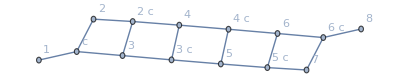

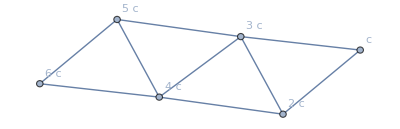

Clique Tree Calibrate MaxProduct test factors: True

```mathematica
(*KEEP THIS TEST SEPARATE AS TAKES 20 MINS TO RUN*)
ocr=Get[datadirectory<>"computeExactMarginalsBP_ocr.txt"];
maxMarginals=computeExactMarginalsBP[ocr,{},True,"Kruskal",True];
MAPAssignment=maxDecoded[maxMarginals];
Print["Clique Tree Calibrate MaxProduct test factors: ",Last@MAPAssignment=="mornings"]
```